Green 01v234 Rotations (81K)

```mathematica
Import data
```

```mathematica
rotations={"0","0v","180","180v"};
```

```mathematica
validation=Import[NotebookDirectory[]<>"validations_g_01v234_40r-2-40r-2-40r-2-40r-4-256rd0.5-256rd0.5-wd0-lr0.001_48K-wd0.0015_iter_81000_"<>ToString[#]<>".csv"]&/@rotations;
```

```mathematica
validationGE=Import[NotebookDirectory[]<>"validations_ge_01v234_40r-2-40r-2-40r-2-40r-4-256rd0.5-256rd0.5-wd0.0001-lr0.001_24K-lr0.0003_iter_54000_"<>ToString[#]<>".csv"]&/@rotations;
```

## Lots of helpful functions

```mathematica
ConfusionMatrix[gndpre_List]:=With[{categories=Union[Flatten[gndpre]]},Partition[Flatten[Table[Count[gndpre,{row,col}],{row,categories},{col,categories}]],Length[categories]]]
AuxMatrix[m_]:=N[Table[Total[m[[i,All]]]*Total[m[[All,j]]]/Total[Total[m]],{i,1,Length[m]},{j,1,Length[m]}]]
SumProduct[a_,b_]:=Total[Total[Table[a[[i,j]]*b[[i,j]],{i,1,Length[a]},{j,1,Length[b]}]]]
Kappa[m_]:=1-SumProduct[m,w]/SumProduct[w,AuxMatrix[m]]
Kappa2[m_]:=1-SumProduct[m,w2]/SumProduct[w2,AuxMatrix[m]]
w = Table[(i-j)^2,{i,1,5},{j,1,5}];
w2= Table[(i-j)^2,{i,1,2},{j,1,2}];
mapToClass[n1_,n2_,n3_,n4_,data_]:=If[data>n4,4,If[data>n3,3,If[data>n2,2,If[data>n1,1,0]]]];
mapToClass2[n1_,n2_,n3_,n4_,m1_,m2_,m3_,m4_,n_,m_]:=If[n>n4&&m>m4,4,If[n>n3&&m>m3,3,If[n>n2&&m>m2,2,If[n>n1&&m>m1,1,0]]]]
mapToClassDiag[b1_,b2_,b3_,b4_,k_,x_,y_]:=If[y>k*x+b4,4,If[y>k*x+b3,3,If[y>k*x+b2,2,If[y>k*x+b2,2,If[y>k*x+b1,1,0]]]]];
KCMerged[n1_,n2_,n3_,n4_,m1_,m2_,m3_,m4_,data_]:=Kappa[ConfusionMatrix[{#[[2]],mapToClass2[n1,n2,n3,n4,m1,m2,m3,m4,#[[8]],#[[4]]]}&/@data]];
KCMergedDiag[b1_,b2_,b3_,b4_,k_,data_]:=Kappa[ConfusionMatrix[{#[[2]],mapToClassDiag[b1,b2,b3,b4,k,#[[8]],#[[4]]]}&/@data]];
divisionLines2[n1_,n2_,n3_,n4_,m1_,m2_,m3_,m4_]:={
Line[{{n1,m1},{n1,10}}],Line[{{n1,m1},{10,m1}}],
Line[{{n2,m2},{n2,10}}],Line[{{n2,m2},{10,m2}}],
Line[{{n3,m3},{n3,10}}],Line[{{n3,m3},{10,m3}}],
Line[{{n4,m4},{n4,10}}],Line[{{n4,m4},{10,m4}}]
};
divisionLinesDiag[b1_,b2_,b3_,b4_,k_]:={
Line[{{-10,k*-10+b1},{10,k*10+b1}}],
Line[{{-10,k*-10+b2},{10,k*10+b2}}],
Line[{{-10,k*-10+b3},{10,k*10+b3}}],
Line[{{-10,k*-10+b4},{10,k*10+b4}}]
};
getmax[data_]:=data[[Position[data,Max[data[[All,5]]]][[1]][[1]]]];
getmax2[data_]:=data[[Position[data,Max[data[[All,2]]]][[1]][[1]]]];
prepareForListPlot[data_,offset_]:={#[[4]],#[[2]]+0.1*offset+0.1*RandomReal[{0,1}]}&/@data;
selectData[data_,label_]:=Select[data,#[[2]]==label&];
binCountsForLabel[data_,label_]:=BinCounts[selectData[data,label][[All,4]],{-0.2,1.4,0.05}](*/Length[selectData[data,label]]*);
binCountsForData[data_]:=binCountsForLabel[data,#]&/@{0,1,2,3,4};
KCS[n1_,n2_,n3_,n4_,data_]:=Kappa[ConfusionMatrix[{#[[2]],mapToClass[n1,n2,n3,n4,#[[4]]]}&/@data]];
lookForMax[data_,r_]:={#[[1]],#[[2]],#[[3]],#[[4]],KCS[#[[1]],#[[2]],#[[3]],#[[4]],data]}&/@ Table[Sort[RandomReal[{0.3,1},4]],{r}];
```

## Visualize neuron activations for validation set (G)

```mathematica
Manipulate[ListLinePlot[binCountsForData[validation[[x]]],PlotLegends->{0,1,2,3,4},ImageSize->Large,Filling->Axis],{x,Range[Length[rotations]]}]
```

## Random split (G)

```mathematica
numberOfRandomTuples=100;
```

```mathematica
y=lookForMax[validation[[#]],numberOfRandomTuples]&/@Range[Length[rotations]];
```

```mathematica
getmax[y[[#]]]&/@Range[Length[rotations]]//MatrixForm
```

(0.447803 | 0.648875 | 0.825493 | 0.962803 | 0.472436
0.486705 | 0.708495 | 0.773057 | 0.916509 | 0.477365
0.510889 | 0.66542 | 0.752748 | 0.934314 | 0.471123
0.49243 | 0.688072 | 0.841928 | 0.923839 | 0.478698)

so the kappa score for each of the rotations does not exceed 0.48

Merging G and GE by diagonals

```mathematica
merge=Join[validation[[1]],validationGE[[1]],2];
```

```mathematica
yDiag={#[[1]][[1]],#[[1]][[2]],#[[1]][[3]],#[[1]][[4]],
#[[2]][[1]],
KCMergedDiag[#[[1]][[1]],#[[1]][[2]],#[[1]][[3]],#[[1]][[4]],
#[[2]][[1]],merge]}&/@ Table[{Sort[RandomReal[{0,2},4]],{RandomReal[{-1,-0}]}},{numberOfRandomTuples}];
```

```mathematica
Max[yDiag[[All,6]]]
```

0.466509

This kappa is too small to be interesting...

```mathematica
yDiag[[Position[yDiag,Max[yDiag[[All,6]]]][[1]][[1]]]]
```

{0.843697,1.08996,1.23172,1.36741,-0.835063,0.466509}

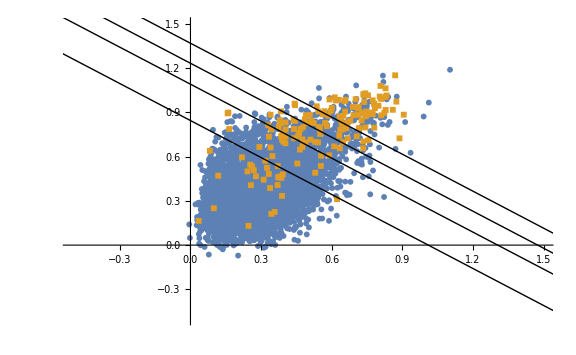

```mathematica
ListPlot[{
Select[merge,#[[2]]==0&][[All,{8,4}]],
Select[merge,#[[2]]==4&][[All,{8,4}]]
},PlotRange->{{-0.5,1.5},{-0.5,1.5}},ImageSize->Large,PlotMarkers->{Automatic,6},Epilog->divisionLinesDiag[
0.8436973224303048,1.0899594646866797,1.231717104401648,1.3674089336378845,-0.8350627987068473
]]
```

Average/minimum/maximum/harmonic mean of rotations (G)

```mathematica
getAveraged[data_,func_]:={#[[1]],#[[2]],#[[3]],func[{#[[4]],#[[8]],#[[12]],#[[16]]}]}&/@Join[data[[1]],data[[2]],data[[3]],data[[4]],2];
```

we tried to take the maximum, minimum, harmonic mean and arithmetic mean of the activations of each image in the validation set and then look for good thresholds. The 
best results are obtained on harmonic mean and arithmetic mean.

```mathematica
mean=getAveraged[validation,Mean];
minimized=getAveraged[validation,Min];
maximized=getAveraged[validation,Max];
harmonic=getAveraged[validation,HarmonicMean];
```

```mathematica
yMean=lookForMax[mean,500];
```

```mathematica
getmax[yMean]
```

{0.539834,0.717297,0.760166,0.843286,0.494855}

```mathematica
yMin=lookForMax[minimized,500];
```

```mathematica
getmax[yMin]
```

{0.450731,0.601695,0.700712,0.85457,0.489815}

```mathematica
yMax=lookForMax[maximized,500];
```

```mathematica
getmax[yMax]
```

{0.609044,0.783159,0.892857,0.955836,0.483442}

```mathematica
yH=lookForMax[harmonic,500];
```

```mathematica
getmax[yH]
```

{0.486028,0.664783,0.800827,0.907706,0.49471}

```mathematica
ConfusionMatrix[{#[[2]],mapToClass[
0.5398341165489482,0.7172969181531681,0.7601657583351111,0.8432862979878946
,#[[4]]]}&/@mean]//TableForm
```

4603 | 673 | 81 | 110 | 67
411 | 67 | 11 | 11 | 10
481 | 305 | 62 | 102 | 139
22 | 42 | 14 | 35 | 66
22 | 27 | 17 | 34 | 60

```mathematica
Kappa[%]
```

0.494855

this is the best performing solution. Kappa on private leaderboard is even higher! 0.50

The difference between the activations of non - rotated images and averaged activations is shown below

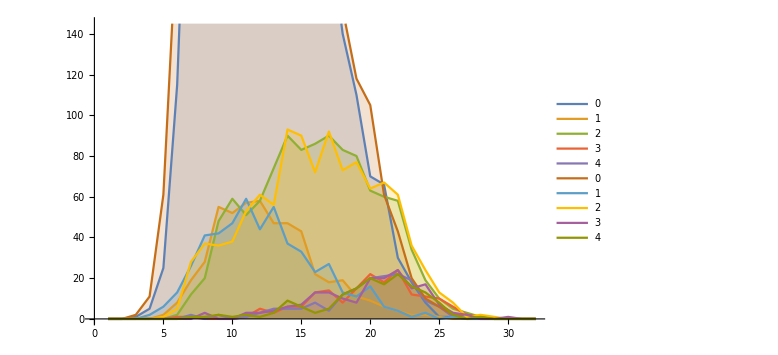

```mathematica
ListLinePlot[Join[binCountsForData[mean],binCountsForData[validation[[1]]]],PlotLegends->{0,1,2,3,4,0,1,2,3,4},ImageSize->Large,Filling->Axis]
```

## Generate the submission CSV (based on averaged activations on G)

```mathematica
prediction=Import[NotebookDirectory[]<>"predictions_g_01v234_40r-2-40r-2-40r-2-40r-4-256rd0.5-256rd0.5-wd0-lr0.001_48K-wd0.0015_iter_81000_"<>ToString[#]<>".csv"]&/@rotations;
```

```mathematica
Pmerge=Join[prediction[[1]],prediction[[2]],prediction[[3]],prediction[[4]],2];
```

```mathematica
Paveraged={#[[1]],Mean[{#[[2]],#[[4]],#[[6]],#[[8]]}]}&/@Pmerge;
```

```mathematica
PaveragedMapped={#[[1]],mapToClass[
0.5398341165489482,0.7172969181531681,0.7601657583351111,0.8432862979878946
,#[[2]]]}&/@Paveraged
```

{{10000_left.jpeg,1},{10000_right.jpeg,0},{10001_left.jpeg,0},{10001_right.jpeg,2},{10002_left.jpeg,3},{10002_right.jpeg,0},{10004_left.jpeg,1},{10004_right.jpeg,0},{10005_left.jpeg,1},{10005_right.jpeg,0},{10006_left.jpeg,1},53554,{9991_right.jpeg,0},{9994_left.jpeg,0},{9994_right.jpeg,0},{9995_left.jpeg,1},{9995_right.jpeg,2},{9997_left.jpeg,1},{9997_right.jpeg,0},{999_left.jpeg,0},{999_right.jpeg,0},{9_left.jpeg,1},{9_right.jpeg,4}}
 |  |  |  |

```mathematica
Export[NotebookDirectory[]<>"submission_g_01v234_40r-2-40r-2-40r-2-40r-4-256rd0.5-256rd0.5-wd0-lr0.001_48K-wd0.0015_iter_81000_ave_0.539834-0.717297-0.760166-0.843286.csv",PaveragedMapped]
```

Note that the generated CSV doesn’t have the header required by Kaggle, and file names include .jpeg extension which should be removed